# Solution for the spectra of the masses of the glueball according to the paper by Zhang, et al. 2022

Let’s first define the generic Equation to solve and the shape of the potential in terms of A and  functions.

```mathematica
F[V_Symbol]:=-S''[z]+V[z]*S[z];
V[A_Symbol,ϕ_Symbol]:=(3*D[D[A[z],z],z]+3/z^2-D[D[ϕ[z],z],z])/2+(3*D[A[z],z]-3/z-D[ϕ[z],z])^2/4;
```

## Model A

```mathematica
a=1;
Ae1[z_]:=-a*z^2;
ϕe1[z_]:=z*Sqrt[3*a*(3+2*a*z^2)]+3/2*Sqrt[6]ArcSinh[Sqrt[2*a/3]*z];
S11=Ae1[z]-Sqrt[1/6]*ϕe1[z];
S12=Sqrt[8/3]*ϕe1[z];
As1[z_]:=S11;
ϕs1[z_]:=S12;
v1=V[As1,ϕs1];
Z1[z_]:=v1;
NDEigenvalues[F[Z1],S[z],{z,0,3},4]
NDEigenvalues[F[Z1],S[z],{z,0,8},4]
NDEigenvalues[F[Z1],S[z],{z,0,30},4]
NDEigenvalues[F[Z1],S[z],{z,0,100},4]
NDEigenvalues[F[Z1],S[z],{z,0,1000},4]
NDEigenvalues[F[Z1],S[z],{z,0,9000},4]
ListPlot[NDEigenvalues[F[Z1],S[z],{z,0,3},4],Frame->True,PlotFit->Automatic.08,PlotStyle->Directive[White,Thick]]
```

{208.787,247.561,286.687,326.154}

{208.86,251.368,295.139,340.024}

{218.387,367.887,386.358,648.112}

{204.372,858.833,2705.14,5816.7}

{4813.96,73208.5,257998.,569196.}

{379898.,5.91989×10^6,2.08879×10^7,4.60949×10^7}

-Graphics-

## Model B

```mathematica
b=1;
Ae2[z_]:=-Log[(2^(3/8)*3^(1/8)*Gamma[5/4]*BesselI[1/4,(b*z^2)/(Sqrt[6])])/(b^(1/4)*Sqrt[z])];
ϕe2[z_]:=b*z^2;
S21=Ae2[z]-Sqrt[1/6]*ϕe2[z];
S22=Sqrt[8/3]*ϕe2[z];
As2[z_]:=S21;
ϕs2[z_]:=S22;
v2=V[As2,ϕs2];
Z2[z_]:=v2;
NDEigenvalues[F[Z2],S[z],{z,0,3},4]
NDEigenvalues[F[Z2],S[z],{z,0,8},4]
NDEigenvalues[F[Z2],S[z],{z,0,30},4]
NDEigenvalues[F[Z2],S[z],{z,0,100},4]
NDEigenvalues[F[Z2],S[z],{z,0,1000},4]
ListPlot[NDEigenvalues[F[Z2],S[z],{z,0,3},4],Frame->True,PlotFit->Automatic.08,PlotStyle->Directive[White,Thick]]
```

{24.3223,38.2805,52.9945,68.2349}

{24.3439,38.4099,53.3577,69.5781}

General::munfl: 1/((1.25188×10^156)^2) is too small to represent as a normalized machine number; precision may be lost.

{25.1474,43.8464,83.2238,144.46}

General::munfl: 1/((8.53561×10^163)^2) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((3.26278×10^208)^2) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((3.60382×10^185)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{23.0608,111.668,420.182,938.876}

General::munfl: 295.501 5.79679680339313×10^-695 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 414.976 2.0882537275984×10^-1094 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 916.676 5.48456112507487×10^-3154 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{758.753,12021.2,40396.7,89148.2}

-Graphics-

## Study of the hard wall for Model B

We have just seen that the numeric results diverge as the upper bound of z increases, so it looks like we have to add a hard wall on top of the already soft wall model. So let’s see which is the upper bound of z that gives us the best value for .08. This is done now for Model B.

```mathematica
Eigen1=Table[NDEigenvalues[F[Z2],S[z],{z,0,z0},4],{z0,0.5,500,0.5}];
```

General::munfl: 1/((1.25188×10^156)^2) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((2.47416×10^161)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

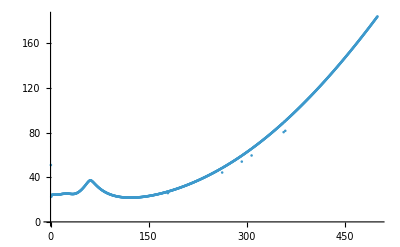

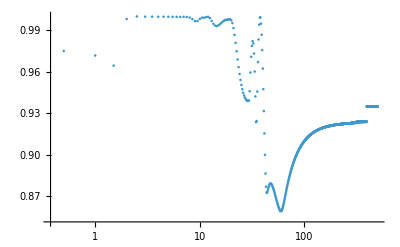

{{2.5,0.999778}}

```mathematica
trajectories=Table[Table[{b,Extract[Extract[Eigen1,a],b]},{b,1,4}],{a,1,Length[Eigen1]}];
R2fits=Table[LinearModelFit[Extract[trajectories,a],x,x]["RSquared"],{a,1,Length[trajectories]}];
z0values=Table[z0,{z0,0.5,500,0.5}];
ListPlot[Table[{Extract[z0values,i],Extract[Extract[Eigen1,i],1]},{i,1,Length[z0values]}],PlotRange->All,AxesLabel->{"", ""}]
ListPlot[Table[{Extract[z0values,i],Extract[R2fits,i]},{i,1,Length[z0values]}],ScalingFunctions->{"Log",None},PlotRange->All,AxesLabel->{"",""}]
Z0Max=MaximalBy[Table[{Extract[z0values,i],Extract[R2fits,i]},{i,1,Length[z0values]}],Last]
```

Now we have just seen that the hard wall is around 2, let’s repeat the process with more precision around  2.

```mathematica
Eigen1prec=Table[NDEigenvalues[F[Z2],S[z],{z,0,z0},4],{z0,1.5,2.5,0.001}];
```

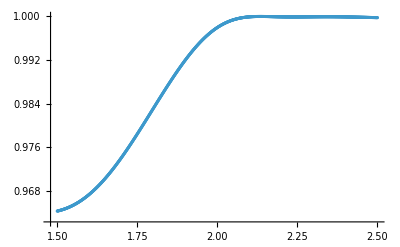

2.135

```mathematica
trajectoriesprec=Table[Table[{b,Extract[Extract[Eigen1prec,a],b]},{b,1,4}],{a,1,Length[Eigen1prec]}];
R2fitsprec=Table[LinearModelFit[Extract[trajectoriesprec,a],x,x]["RSquared"],{a,1,Length[trajectoriesprec]}];
z0valuesprec=Table[z0,{z0,1.5,2.5,0.001}];
ListPlot[Table[{Extract[z0valuesprec,i],Extract[R2fitsprec,i]},{i,1,Length[z0valuesprec]}],PlotRange->All,AxesLabel->{"",""}]
Z0Maxprec=Extract[Extract[MaximalBy[Table[{Extract[z0valuesprec,i],Extract[R2fitsprec,i]},{i,1,Length[z0valuesprec]}],Last],1],1]
```

## Study of the Hard Wall for Model A

Now let’s repeat the process for model A.

```mathematica
Eigen2=Table[NDEigenvalues[F[Z1],S[z],{z,0,z0},4],{z0,0.5,500,0.5}];
```

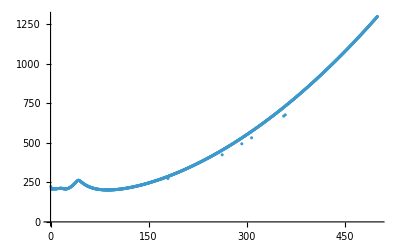

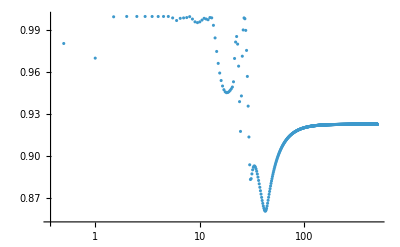

{{2.,0.999993}}

```mathematica
trajectories=Table[Table[{b,Extract[Extract[Eigen2,a],b]},{b,1,4}],{a,1,Length[Eigen2]}];
R2fits=Table[LinearModelFit[Extract[trajectories,a],x,x]["RSquared"],{a,1,Length[trajectories]}];
z0values=Table[z0,{z0,0.5,500,0.5}];
ListPlot[Table[{Extract[z0values,i],Extract[Extract[Eigen2,i],1]},{i,1,Length[z0values]}],PlotRange->All,AxesLabel->{"", ""}]
ListPlot[Table[{Extract[z0values,i],Extract[R2fits,i]},{i,1,Length[z0values]}],ScalingFunctions->{"Log",None},PlotRange->All,AxesLabel->{"",""}]
Z0Max=MaximalBy[Table[{Extract[z0values,i],Extract[R2fits,i]},{i,1,Length[z0values]}],Last]
```

```mathematica
Eigen2prec=Table[NDEigenvalues[F[Z1],S[z],{z,0,z0},4],{z0,1.5,2.5,0.001}];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
trajectoriesprec=Table[Table[{b,Extract[Extract[Eigen2prec,a],b]},{b,1,4}],{a,1,Length[Eigen2prec]}];
R2fitsprec=Table[LinearModelFit[Extract[trajectoriesprec,a],x,x]["RSquared"],{a,1,Length[trajectoriesprec]}];
z0valuesprec=Table[z0,{z0,1.5,2.5,0.001}];
ListPlot[Table[{Extract[z0valuesprec,i],Extract[R2fitsprec,i]},{i,1,Length[z0valuesprec]}],PlotRange->All,AxesLabel->{"",""}]
Z0Maxprec=Extract[Extract[MaximalBy[Table[{Extract[z0valuesprec,i],Extract[R2fitsprec,i]},{i,1,Length[z0valuesprec]}],Last],1],1]
```